## First - two masses and three strings

```mathematica
l1 = 1;
l12 = 2;
l2 = 3;
k =1;
```

```mathematica
solution = DSolve[{
x1''[t] == -k(x1[t] -l1) + k(x2[t]-x1[t]-l12),
x2''[t] == -k(x2[t] - l2),
x1[0] == 1,
x1'[0] == 0,
x2[0] == 2,
x2'[0] == 0
},
{x1[t], x2[t]}, t
]
```

{{x1[t]→1/2 (-2 Cos[t]+6 Cos[t]^2+3 Cos[√2 t]-5 Cos[√2 t]^2+6 Sin[t]^2-5 Sin[√2 t]^2),x2[t]→-Cos[t]+3 Cos[t]^2+3 Sin[t]^2}}

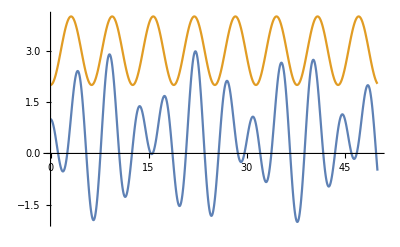

```mathematica
Plot[{solution[[1,1, 2]], solution[[1,2, 2]]}, {t, 0, 50}]
```